# ENTROPY CALCULATIONS

## Basics

The first line makes mathematica arrays look like matrices at the outputs. 

The rest is a function that traces out a subsystem of quDits from a N-quDit system.  dTraceSystem has 3 arguments, the density matrix ρ, the list of qudits to trace out, e.g. {2, 3} and the dimension d of the qudits. This code was taken from the Wolfram Library Archive and it is called 	
“Partial Trace of a MultiquDit System” by Mark Tame.
(https://library.wolfram.com/infocenter/MathSource/8763/)

```mathematica
ClearAll["Global`*"]
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
dTraceSystem[D_, s_, dimen_]:= (

Qudits=Reverse[Sort[s]];
TrkM=D;
dim=dimen;

z=(Dimensions[Qudits][[1]]+1);

For[q=1,q<z,q++,
n=Log[dim,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qudits[[q]];
If[k==n,
TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
 ],

For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<dim^n+1,i++,
If[IntegerDigits[i-1,dim,n][[n]]≠IntegerDigits[i-1,dim,n][[n-j-1]] && Count[b, i]  ==0, 
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)];
c=Range[dim^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)}];
M=M[[perm,perm]];
 ]    
];
   ];

TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
]
]
]

;Return[TrkM])
```

## Functions for Entropies

```mathematica
vonNeummanbeta[rho_]:=(
{vals,vecs}=Refine[Eigensystem[rho]];
M=Refine[Transpose[vecs]];
Inverse[M];
DG=Refine[DiagonalMatrix[vals]];
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD=Refine[MatrixFunction[F,DG]];
Return[ Simplify[-Tr[M.FD.Inverse[M]]]];
)
vonNeumann[densmatr_]:=(
Fv2[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
Return[Simplify[-Tr[MatrixFunction[Fv2,densmatr]]]])

ConditionalS[densmatr_,sublist_]:=Simplify[vonNeumann[densmatr]-vonNeumann[dTraceSystem[densmatr,sublist,2]]];
Renyi[denmatr_,a_]:=(
Functionaling[x_]:=x^a ;
matrixtrans=Refine[MatrixFunction[Functionaling,denmatr]];
Return[Simplify[(1/(1-a))Log[Tr[matrixtrans]]]];
)

Unified[densmatr_,r_,s_]:= (Tr[densmatr^r]^s-1)/(s-r*s);

Tsalis[densmatr_,r_]:=(
{valsT,vecsT}=Refine[Eigensystem[densmatr]];
MT=Refine[Transpose[vecsT]];
Inverse[MT];
DGT=Refine[DiagonalMatrix[valsT]];
FT[x_]:=Piecewise[{{x^r,x≥0}},null];
FDT=Refine[MatrixFunction[FT,DGT]];
Return[ Simplify[(Tr[MT.FDT.Inverse[MT]]-1)/(1-r)]];
);
QuadraticEntropy[densmatr_]:=(
{valsQ,vecsQ}=Refine[Eigensystem[densmatr]];
M=Refine[Transpose[vecsQ]];
Inverse[M];
DGQ=Refine[DiagonalMatrix[valsQ]];
FQ[x_]:=Piecewise[{{x^2,x≥0}},null];
FDQ=Refine[MatrixFunction[FQ,DGQ]];
Return[ Simplify[1-Tr[M.FDQ.Inverse[M]]]];
);
ConditionalQ[densmatr_,sublist_]:=Simplify[QuadraticEntropy[densmatr]-QuadraticEntropy[dTraceSystem[densmatr,sublist,2]]];

RelativeEntropy[dm1_,dm2_]:=(
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
matr=dm1.MatrixFunction[K,dm2];
termo=-Tr[matr]-vonNeumann[dm1];
Return[Simplify[Limit[termo,ε-> -Infinity]]]
)
```

## Calculation Details

### vonNeumman1

```mathematica
psi1=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho1=KroneckerProduct[psi1,ConjugateTranspose[psi1]]
{vals1,vecs1}=Eigensystem[rho1]
M1=Transpose[vecs1]
Det[M1]
Inverse[M1]
DG1=DiagonalMatrix[vals1]
M1.DG1.Inverse[M1]==rho1
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD1=MatrixFunction[F,DG1];
L1=-Tr[M1.FD1.Inverse[M1]]
Refine[L1==vonNeumman[rho1]]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

{{1,0,0,0},{{0,ⅈ,1,0},{0,0,0,1},{0,-ⅈ,1,0},{1,0,0,0}}}

(0 | 0 | 0 | 1
ⅈ | 0 | -ⅈ | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

2 ⅈ

(0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

0

0==vonNeumman[{{0,0,0,0},{0,1/2,ⅈ/2,0},{0,-ⅈ/2,1/2,0},{0,0,0,0}}]

### vonNeumann2

{{s,0},{0,1-s}}

{{1-s,s},{{0,1},{1,0}}}

{{s Log[s],0},{0,(1-s) Log[1-s]}}

-(1-s) Log[1-s]-s Log[s]

-(1-s) Log[1-s]-s Log[s]==vonNeumman[{{s,0},{0,1-s}}]

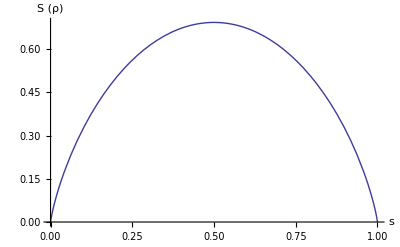

```mathematica
$Assumptions = s∈ Reals && 0<s<1;
rho2=Refine[{{s,0},{0,1-s}}]
{vals2,vecs2}=Refine[Eigensystem[rho2]]
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD2=Refine[MatrixFunction[F,rho2]]
L2=-Tr[FD2]
Refine[L2== vonNeumman[rho2]]
Plot[L2,{s,0,1},AxesLabel->{"s", "S (ρ)" }]
```

### ConditionalEntropy3

(Cos[θ]
0
0
Sin[θ])

(Cos[θ]^2 | 0 | 0 | Cos[θ] Sin[θ]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2)

{{1,0,0,0},{{(-1+Csc[θ]^2) Tan[θ],0,0,1},{-Tan[θ],0,0,1},{0,0,1,0},{0,1,0,0}}}

(Cot[θ] | -Tan[θ] | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 1 | 0 | 0)

-Csc[θ] Sec[θ]

(Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2
-Cos[θ] Sin[θ] | 0 | 0 | Cos[θ]^2
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

0

(Cos[θ]^2 | 0
0 | Sin[θ]^2)

2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2)

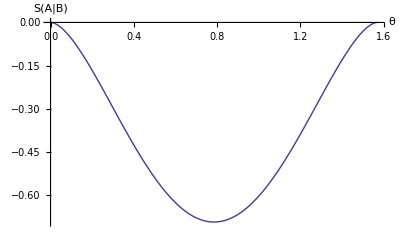

-Log[2]

```mathematica
Clear[θ]
$Assumptions=θ∈Reals && 0<θ<π/2;
chi3={{Cos[θ]},{0},{0},{Sin[θ]}}
sigma3=Refine[KroneckerProduct[chi3,ConjugateTranspose[chi3]]]
{values3,vecs3}=Eigensystem[sigma3]
M3=Simplify[Transpose[vecs3]]
FullSimplify[Det[M3]]
M3inv=Simplify[Inverse[M3]]
diag3=DiagonalMatrix[values3]
sigma3== M3.diag3.M3inv
vonNeumann[sigma3]
sigmaA=dTraceSystem[sigma3,{2},2]
L3=ConditionalS[sigma3,{2}]
Plot[L3,{θ,0,π/2},AxesLabel->{"θ","S(A|B)"}]
Refine[L3,θ== π/4]
```

### Renyi4

```mathematica
$Assumptions = α∈ Reals && α>0 && α≠ 1;
psi4=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho4=KroneckerProduct[psi4,ConjugateTranspose[psi4]]
{vals4,vecs4}=Eigensystem[rho4]
M4=Transpose[vecs4]
Det[M4]
Inverse[M4]
DG4=DiagonalMatrix[vals4]
M4.DG4.Inverse[M4]==rho4
Functionaling4[x_]:=x^α;
matrixtrans4=Refine[MatrixFunction[Functionaling4,DG4]]
matrixtrans4next=M4.matrixtrans4.Inverse[M4]
ppp=Tr[matrixtrans4next]
Log[ppp]
Log[ppp]== Renyi[rho4,α]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

{{1,0,0,0},{{0,ⅈ,1,0},{0,0,0,1},{0,-ⅈ,1,0},{1,0,0,0}}}

(0 | 0 | 0 | 1
ⅈ | 0 | -ⅈ | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

2 ⅈ

(0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

1

0

True

### Renyi5

(s | 0
0 | 1-s)

(s^α | 0
0 | (1-s)^α)

Log[(1-s)^α+s^α]/(1-α)

True

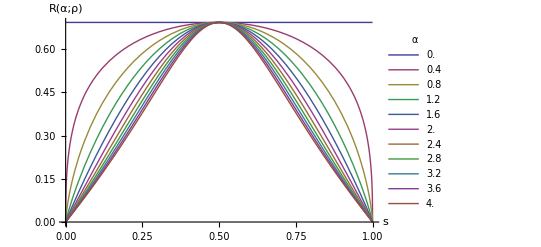

-Graphics3D-

```mathematica
Clear[α,s]
$Assumptions = α∈ Reals && α>0 && α≠ 1;
$Assumptions = s∈ Reals && 0<s<1;
rho5= {{s,0},{0,1-s}}
function5[x_]:=x^α
finalmatrix=MatrixFunction[function5,rho5]
L5=Log[Tr[finalmatrix]]/(1-α)
L5== Renyi[rho5,α]
Plot[Evaluate@Table[L5,{α,0,4,0.4}],{s,0,1},PlotLegends->LineLegend[Table[α,{α,0,4,0.4}],LegendLabel->α],AxesLabel->{"s","R(α;ρ)"}]
Plot3D[L5,{s,0,1},{α,0,15},AxesLabel->{"s","α","R"}]
```

### Relative entropy6

```mathematica
psi6=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho6=KroneckerProduct[psi6,ConjugateTranspose[psi6]]
sigma6= {{1/2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/2}}
Eigensystem[sigma6]
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
matr6g=MatrixFunction[K,sigma6]
matrix6=rho6.matr6g
L9=-Limit[Tr[matrix6],ε-> -Infinity]
L9== RelativeEntropy[rho6,sigma6]
RelativeEntropy[sigma6,rho6]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

(1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/2)

{{1/2,1/2,0,0},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}

(-Log[2] | 0 | 0 | 0
0 | ε | 0 | 0
0 | 0 | ε | 0
0 | 0 | 0 | -Log[2])

(0 | 0 | 0 | 0
0 | ε/2 | (ⅈ ε)/2 | 0
0 | -(ⅈ ε)/2 | ε/2 | 0
0 | 0 | 0 | 0)

∞

True

∞

### Tsallis7

```mathematica
Clear[q]
$Assumptions = q∈ Reals && q>0 && q≠ 1;
psi7=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}};
rho7=KroneckerProduct[psi7,ConjugateTranspose[psi7]];
{vals7,vecs7}=Eigensystem[rho7];
M7=Transpose[vecs7];
Det[M7];
Inverse[M7];
DG7=DiagonalMatrix[vals7]
M7.DG7.Inverse[M7]==rho7
F7[x_]:=x^q;
FD7=Simplify[MatrixFunction[F7,DG7]]
trace7=Tr[M7.FD7.Inverse[M7]]
(trace7-1)/(1-q)
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

1

0

### Tsallis8

(s | 0
0 | 1-s)

(s^q | 0
0 | (1-s)^q)

(-1+(1-s)^q+s^q)/(1-q)

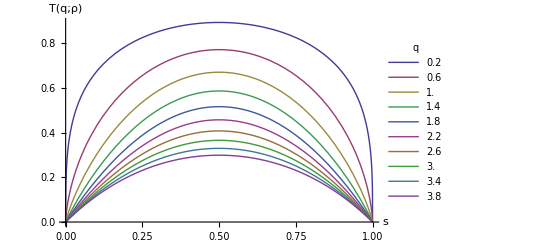

-Graphics3D-

```mathematica
Clear[q,s]
$Assumptions = q∈ Reals && q>0 && q≠ 1;
$Assumptions = s∈ Reals && 0<s<1;
rho8= {{s,0},{0,1-s}}
function7[x_]:=x^q
matr8=MatrixFunction[function7,rho8]
L8=((Tr[matr8])-1)/(1-q)
Plot[Evaluate@Table[L8,{q,0.3,4,0.4}],{s,0,1},PlotLegends->LineLegend[Table[q,{q,0.2,4,0.4}],LegendLabel->q],AxesLabel->{"s","T(q;ρ)"}]
Plot3D[L8,{s,0,1},{q,0,15},AxesLabel->{"s","q","T"}]
```

### Relative

```mathematica
Clear[s1,s2,t,rho1,L,sigma1]
$Assumptions = s1∈ Reals && 0<=s1<=1;
$Assumptions = s2∈ Reals && 0<=s2<=1;
$Assumptions = t∈ Reals && 0<t<π/2;
$Assumptions = f∈ Reals && 0<f<π/2;
ket0={{1},{0}};
bra0=ConjugateTranspose[ket0];
ket1={{0},{1}};
bra1=ConjugateTranspose[ket1];
ket00=KroneckerProduct[ket0,ket0];
bra00=ConjugateTranspose[ket00];
ket01=KroneckerProduct[ket0,ket1];
bra01=ConjugateTranspose[ket01];
ket10=KroneckerProduct[ket1,ket0];
bra10=ConjugateTranspose[ket01];
ket11=KroneckerProduct[ket1,ket1];
bra11=ConjugateTranspose[ket11];
rho1=Cos[t]^2*(ket0.bra0)+Sin[t]^2*(ket1.bra1)
sigma1=Cos[f]^2*(ket0.bra0)+Sin[f]^2*(ket1.bra1)
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
secondmatrix=Simplify[MatrixFunction[K,sigma1]]
secondterm = Tr[rho1.secondmatrix]
firstterm = Refine[vonNeumann[rho1],t∈ Reals && 0<t<π/2]
L8=firstterm-secondterm
L8test=Refine[RelativeEntropy[rho1,sigma1],0<t<π/2&& 0<f<π/2]
L8sigmarho=Refine[RelativeEntropy[sigma1,rho1],0<t<π/2&& 0<f<π/2]
Limit[L8,t->0]
Limit[L8,f->0]
Limit[L8sigmarho,t->0]
Limit[L8sigmarho,f->0]
Plot3D[L8,{t,0,π/2},{f,0,π/2}]
```

(Cos[t]^2 | 0
0 | Sin[t]^2)

(Cos[f]^2 | 0
0 | Sin[f]^2)

(2 Log[Cos[f]] | 0
0 | 2 Log[Sin[f]])

2 Cos[t]^2 Log[Cos[f]]+2 Log[Sin[f]] Sin[t]^2

-2 Cos[t]^2 Log[Cos[t]]-2 Log[Sin[t]] Sin[t]^2

-2 Cos[t]^2 Log[Cos[f]]-2 Cos[t]^2 Log[Cos[t]]-2 Log[Sin[f]] Sin[t]^2-2 Log[Sin[t]] Sin[t]^2

Cos[t]^2 (-2 Log[Cos[f]]+2 Log[Cos[t]])+(-2 Log[Sin[f]]+2 Log[Sin[t]]) Sin[t]^2

Cos[f]^2 (2 Log[Cos[f]]-2 Log[Cos[t]])+(2 Log[Sin[f]]-2 Log[Sin[t]]) Sin[f]^2

-2 Log[Cos[f]]

∞ Sin[t]^2

∞

-2 Log[Cos[t]]

-Graphics3D-

### Relativetest

(s | 0
0 | 1-s)

(Cos[θ]^2 | 0
0 | Sin[θ]^2)

1/2 (-Log[1-s]-Log[s]+2 Log[Cos[θ]]+Cos[2 θ] (Log[1-s]-Log[s]+2 Log[Cot[θ]])+2 Log[Sin[θ]])

-(-1+s) Log[1-s]+s Log[s]+2 (-s Log[Cos[θ]]+Log[Csc[θ]]+s Log[Sin[θ]])

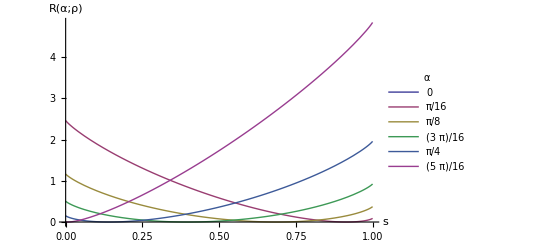

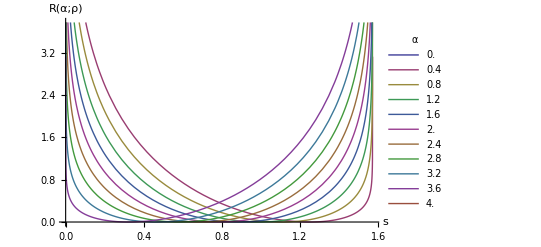

-Graphics3D-

```mathematica
Clear[s,θ]
$Assumptions=s∈Reals && 0<s<1 && θ∈Reals && 0<θ<π/2;
rho6 = {{s,0},{0,1-s}}
sigma6={{Cos[θ]^2,0},{0,Sin[θ]^2}}
L7=RelativeEntropy[sigma6,rho6]
L6= RelativeEntropy[rho6,sigma6]
Plot[Evaluate@Table[L6,{θ,0,π /2,π/16+0.1}],{s,0,1},PlotLegends->LineLegend[Table[ θ,{θ,0,π /2,π/16}],LegendLabel->α],AxesLabel->{"s","R(α;ρ)"}]
Plot[Evaluate@Table[L6,{s,0,1,0.1}],{θ,0,π/2},PlotLegends->LineLegend[Table[α,{α,0,4,0.4}],LegendLabel->α],AxesLabel->{"s","R(α;ρ)"}]
Plot3D[L6,{s,0,1},{θ,0,π/2}]
```

### Relative Entropy Example

```mathematica
Clear[s1,s2,t,rho2,L,sigma2]
$Assumptions = s1∈ Reals && 0<s1<1;
$Assumptions = s2∈ Reals && 0<s2<1;
ket0={{1},{0}};
bra0=ConjugateTranspose[ket0];
ket1={{0},{1}};
bra1=ConjugateTranspose[ket1];
ket00=KroneckerProduct[ket0,ket0];
bra00=ConjugateTranspose[ket00];
ket01=KroneckerProduct[ket0,ket1];
bra01=ConjugateTranspose[ket01];
ket10=KroneckerProduct[ket1,ket0];
bra10=ConjugateTranspose[ket01];
ket11=KroneckerProduct[ket1,ket1];
bra11=ConjugateTranspose[ket11];
rho2=s1*(ket0.bra0)+(1-s1)*(ket1.bra1)
sigma2=s2*(ket0.bra0)+(1-s2)*(ket1.bra1)
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];

secondmatrix=Simplify[MatrixFunction[K,sigma2]]
secondterm = Tr[rho2.secondmatrix]
firstterm = Refine[vonNeumann[rho2],0<s1<1]
L8=firstterm-secondterm
Plot3D[L8,{s1,0,1},{s2,0,1}]

secondmatrix2=Refine[MatrixFunction[K,rho2],0<s1<1]
secondterm2= Tr[sigma2.secondmatrix]
firstterm2 = Refine[vonNeumann[sigma2],0<s2<1]
L82=firstterm2-secondterm2
```

(s1 | 0
0 | 1-s1)

(s2 | 0
0 | 1-s2)

(Log[s2] | 0
0 | Log[1-s2])

(1-s1) Log[1-s2]+s1 Log[s2]

(-1+s1) Log[1-s1]-s1 Log[s1]

(-1+s1) Log[1-s1]-s1 Log[s1]-(1-s1) Log[1-s2]-s1 Log[s2]

-Graphics3D-

(Log[s1] | 0
0 | Log[1-s1])

(1-s2) Log[1-s2]+s2 Log[s2]

(-1+s2) Log[1-s2]-s2 Log[s2]

-(1-s2) Log[1-s2]+(-1+s2) Log[1-s2]-2 s2 Log[s2]

### Relative

```mathematica
Clear[t,u,ε,psi,rho]
$Assumptions=t∈Reals && 0<t<π/2;
$Assumptions=u∈Reals && 0<u<π/2;
psit={{Cos[t]},{0},{0},{Sin[t]}};
rhot=Refine[KroneckerProduct[psit,ConjugateTranspose[psit]],t∈Reals ];
psi={{1/Sqrt[2]},{0},{0},{1/Sqrt[2]}};
rho=KroneckerProduct[psi,ConjugateTranspose[psi]];
psitest={{1/2},{0},{0},{Sqrt[3]/2}};
rhotest=KroneckerProduct[psitest,ConjugateTranspose[psitest]];
{vals,vecs}=FullSimplify[Refine[Eigensystem[rhot]]];
M=FullSimplify[Refine[Transpose[vecs]]];
InveM=FullSimplify[Inverse[M]];
Kappa[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
DG=Refine[DiagonalMatrix[vals]];
RelativeEntropy[rho,rhotest]
```

∞

### Quadratic Conditional Wrong

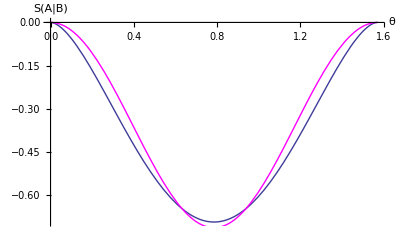

```mathematica
Clear[θ,L3,L4]
$Assumptions=θ∈Reals && 0<θ<π/2;
chi3={{Cos[θ]},{0},{0},{Sin[θ]}};
sigma3=Refine[KroneckerProduct[chi3,ConjugateTranspose[chi3]]];
{values3,vecs3}=Simplify[Eigensystem[sigma3]];
M3=Simplify[Transpose[vecs3]];
FullSimplify[Det[M3]];
M3inv=Simplify[Inverse[M3]];
diag3=DiagonalMatrix[values3];
sigma3== M3.diag3.M3inv;
vonNeumann[sigma3];
sigma3A=dTraceSystem[sigma3,{2},2];
L3=ConditionalS[sigma3,{2}];
L4 =Refine[Tsalis[sigma3,t]-Tsalis[sigma3A,t],t==2.8];
p4=Plot[L4,{θ,0,π/2},AxesLabel->{"θ","QS(A|B)"},PlotStyle->Magenta];
p3=Plot[L3,{θ,0,π/2},AxesLabel->{"θ","S(A|B)"}];
Refine[L3,θ== π/4];
Show[p3,p4]
```

### WernerStateConditional

-Log[2]+3/4 (-1+s) Log[(1-s)/4]-1/4 (1+3 s) Log[1/4 (1+3 s)]

0.549306

0.747614

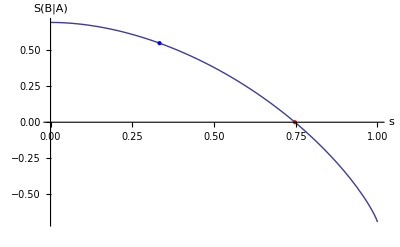

```mathematica
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
{Wvals,Wvecs}=Eigensystem[WernerState];
Mw=Refine[Transpose[Wvecs]];
Det[Mw];
Inverse[Mw];
DGw=Refine[DiagonalMatrix[Wvals]];
WernerState==Simplify[Mw.DG.Inverse[Mw]];
Fw[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FDw=Refine[MatrixFunction[Fw,DGw]];

Simplify[-Tr[Mw.FDw.Inverse[Mw]]]==Simplify[vonNeumann[WernerState]];
Simplify[vonNeumann[WernerState]];
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];
CSofWerner=vonNeumann[WernerState]-vonNeumann[WernerStateA]
Entanglementsvalue=N[Refine[CSofWerner,s==1/3]]
zerocondwerner=s/.FindRoot[CSofWerner,{s,0.7}]

plot1=Plot[CSofWerner,{s,0,1},AxesLabel->{"s","S(B|A)"},GridLines->{{{1/3,Dashed}},{{Entanglementsvalue,Dashed}}},Epilog->{{Blue,PointSize@Large,Point[{1/3,Entanglementsvalue}]},{Red,PointSize@Large,Point[{zerocondwerner,0}]}}]
```

### WernerStateConditionalTsallis

```mathematica
Clear[s,x,q];
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];

{valsT,vecsT}=Refine[Eigensystem[WernerState]];
MT=Refine[Transpose[vecsT]];
Inverse[MT];
DGT=Refine[DiagonalMatrix[valsT]];
FT[y_]:=Piecewise[{{y^x,y≥0}},null];
FDT=Refine[MatrixFunction[FT,DGT]];
MT.FDT.Inverse[MT];

Firstterm=(Tr[MT.FDT.Inverse[MT]]-1)/(1-x);

FDT2=Refine[MatrixFunction[FT,WernerStateA]];
Secondterm=(Tr[FDT2]-1)/(1-x);
ResultingT=Simplify[(Firstterm-Secondterm)/(1+(1-x)*Secondterm)];

examplidionT=Refine[ResultingT,x==0.3]
s/.FindRoot[examplidionT,{s,0.9}];

Plot[Evaluate@Table[ResultingT,{x,0.3,4,0.4}],{s,0,1},PlotLegends->LineLegend[Table[x,{x,0.3,4,0.4}],LegendLabel->x],AxesLabel->{"s","T(q;ρ)"}];
EntanglementLimitValueT=Refine[ResultingT,s==1/3];
Plot[EntanglementLimitValueT,{x,0,100}];
```

-0.58018 (2.46229-3 (1-s)^0.3-(1+3 s)^0.3)

### WernerStateConditionalRenyi

(Log[2^(1-α)]-Log[4^-α (3 (1-s)^α+(1+3 s)^α)])/(-1+α)

(Log[2^(1-α)]-Log[4^-α (3 (1-s)^α+(1+3 s)^α)])/(-1+α)

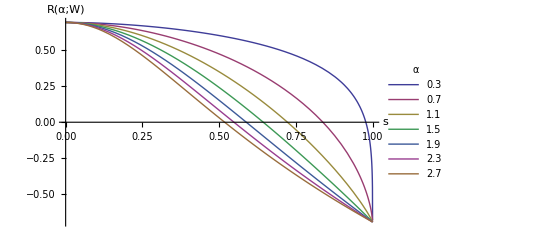

-1.42857 (0.485203-Log[0.659754 (3 (1-s)^0.3+(1+3 s)^0.3)])

0.978043

(Log[2^(1-α)]-Log[4^-α (2^α+2^α 3^(1-α))])/(-1+α)

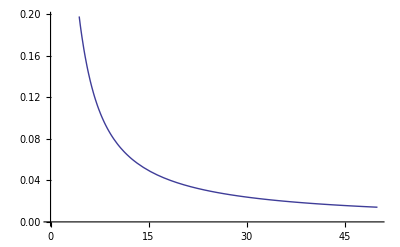

```mathematica
Clear[α,s]
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];
CRofWerner=FullSimplify[Renyi[WernerState,α]-Renyi[WernerStateA,α]]
Clear[α]
{valsR,vecsR}=Refine[Eigensystem[WernerState]];
MR=Refine[Transpose[vecsR]];
Inverse[MR];
DGR=Refine[DiagonalMatrix[valsR]];
FR[y_]:=Piecewise[{{y^α,y≥0}},null];
FDR=Refine[MatrixFunction[FR,DGR]];
FDR;
FtermR=Simplify[Log[Tr[MR.FDR.Inverse[MR]]]/(1-α)];

FDR=Refine[MatrixFunction[FR,WernerStateA]];
FDR;
StermR=Simplify[Log[Tr[FDR]]/(1-α)];

ttt=Simplify[FtermR-StermR]



Plot[Evaluate@Table[ttt,{α,0.3,3,0.4}],{s,0,1},PlotLegends->LineLegend[Table[α,{α,0.3,3,0.4}],LegendLabel->α],AxesLabel->{"s","R(α;W)"},]


examplidionS=Refine[CRofWerner,α==0.3]
s/.FindRoot[examplidionS,{s,0.9}]

EntanglementLimitValue=Refine[CRofWerner,s==1/3]
Plot[EntanglementLimitValue,{α,0,50}]
```

### WernerStateConditionalQuadratic Uselless

```mathematica
Clear[s]
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
{Wvals,Wvecs}=Eigensystem[WernerState];
Mw=Refine[Transpose[Wvecs]];
Det[Mw];
Inverse[Mw];
DGw=Refine[DiagonalMatrix[Wvals]];
WernerState==Simplify[Mw.DGw.Inverse[Mw]];
Fw[x_]:=Piecewise[{{x^2,x>0},{0,x==0}},null];
FDw=Refine[MatrixFunction[Fw,DGw]]

Simplify[-Tr[Mw.FDw.Inverse[Mw]]]==Simplify[vonNeumann[WernerState]];
Simplify[vonNeumann[WernerState]];
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];
CSofWerner=vonNeumann[WernerState]-vonNeumann[WernerStateA]
Entanglementsvalue=N[Refine[CSofWerner,s==1/3]]
zerocondwerner=s/.FindRoot[CSofWerner,{s,0.7}]

plot1=Plot[CSofWerner,{s,0,1},AxesLabel->{"s","S(B|A)"},GridLines->{{{1/3,Dashed}},{{Entanglementsvalue,Dashed}}},Epilog->{{Blue,PointSize@Large,Point[{1/3,Entanglementsvalue}]},{Red,PointSize@Large,Point[{zerocondwerner,0}]}}]
```

(1/16 (1-s)^2 | 0 | 0 | 0
0 | 1/16 (1-s)^2 | 0 | 0
0 | 0 | 1/16 (1-s)^2 | 0
0 | 0 | 0 | 1/16 (1+3 s)^2)

-Log[2]+3/4 (-1+s) Log[(1-s)/4]-1/4 (1+3 s) Log[1/4 (1+3 s)]

0.549306

0.747614

-Graphics-